```mathematica
withSpaces[s_]:=StringJoin[Flatten[Join[{Characters[s][[1]]},Table[If[UpperCaseQ[Characters[s][[i]]],{" ",Characters[s][[i]]},Characters[s][[i]]],{i,2,Length[Characters[s]]}]]]]
```

```mathematica
Table[Table[Export["/home/petter/projects/Trainer/data/countries/"<>cont<>"_"<>withSpaces[i]<>".png",
Graphics[Join[{

EdgeForm[Black],Catch[If[#==i,RGBColor[0.1,0.8,0.1],RGBColor[0.3,0.3,0.3]]],CountryData[#,"Polygon"]


}&/@CountryData[cont],
If[CountryData[i,"Area"]<1500,
{Inset[Graphics[{Green,Thickness[0.01],Line[{{-1,0},{1,0}}],Line[{{0,-1},{0,1}}]}],Reverse[CountryData[i,"CenterCoordinates"]]]},
{}]

],ImageSize->2000]]
,{i,Select[CountryData[cont],CountryData[#,"Population"]>10*10^6||cont=="Europe" &]}],{cont,Select[CountryData["Continents"],#≠"Antarctica"&]}]
```

{{/home/petter/projects/Trainer/data/countries/Africa_Algeria.png,/home/petter/projects/Trainer/data/countries/Africa_Angola.png,/home/petter/projects/Trainer/data/countries/Africa_Burkina Faso.png,/home/petter/projects/Trainer/data/countries/Africa_Cameroon.png,/home/petter/projects/Trainer/data/countries/Africa_Chad.png,/home/petter/projects/Trainer/data/countries/Africa_Democratic Republic Congo.png,/home/petter/projects/Trainer/data/countries/Africa_Egypt.png,/home/petter/projects/Trainer/data/countries/Africa_Ethiopia.png,/home/petter/projects/Trainer/data/countries/Africa_Ghana.png,/home/petter/projects/Trainer/data/countries/Africa_Guinea.png,/home/petter/projects/Trainer/data/countries/Africa_Ivory Coast.png,/home/petter/projects/Trainer/data/countries/Africa_Kenya.png,/home/petter/projects/Trainer/data/countries/Africa_Madagascar.png,/home/petter/projects/Trainer/data/countries/Africa_Malawi.png,/home/petter/projects/Trainer/data/countries/Africa_Mali.png,/home/petter/projects/Trainer/data/countries/Africa_Morocco.png,/home/petter/projects/Trainer/data/countries/Africa_Mozambique.png,/home/petter/projects/Trainer/data/countries/Africa_Niger.png,/home/petter/projects/Trainer/data/countries/Africa_Nigeria.png,/home/petter/projects/Trainer/data/countries/Africa_Rwanda.png,/home/petter/projects/Trainer/data/countries/Africa_Senegal.png,/home/petter/projects/Trainer/data/countries/Africa_South Africa.png,/home/petter/projects/Trainer/data/countries/Africa_Sudan.png,/home/petter/projects/Trainer/data/countries/Africa_Tanzania.png,/home/petter/projects/Trainer/data/countries/Africa_Tunisia.png,/home/petter/projects/Trainer/data/countries/Africa_Uganda.png,/home/petter/projects/Trainer/data/countries/Africa_Zambia.png,/home/petter/projects/Trainer/data/countries/Africa_Zimbabwe.png},{/home/petter/projects/Trainer/data/countries/Asia_Afghanistan.png,/home/petter/projects/Trainer/data/countries/Asia_Bangladesh.png,/home/petter/projects/Trainer/data/countries/Asia_Cambodia.png,/home/petter/projects/Trainer/data/countries/Asia_China.png,/home/petter/projects/Trainer/data/countries/Asia_India.png,/home/petter/projects/Trainer/data/countries/Asia_Indonesia.png,/home/petter/projects/Trainer/data/countries/Asia_Iran.png,/home/petter/projects/Trainer/data/countries/Asia_Iraq.png,/home/petter/projects/Trainer/data/countries/Asia_Japan.png,/home/petter/projects/Trainer/data/countries/Asia_Kazakhstan.png,/home/petter/projects/Trainer/data/countries/Asia_Malaysia.png,/home/petter/projects/Trainer/data/countries/Asia_Myanmar.png,/home/petter/projects/Trainer/data/countries/Asia_Nepal.png,/home/petter/projects/Trainer/data/countries/Asia_North Korea.png,/home/petter/projects/Trainer/data/countries/Asia_Pakistan.png,/home/petter/projects/Trainer/data/countries/Asia_Philippines.png,/home/petter/projects/Trainer/data/countries/Asia_Russia.png,/home/petter/projects/Trainer/data/countries/Asia_Saudi Arabia.png,/home/petter/projects/Trainer/data/countries/Asia_South Korea.png,/home/petter/projects/Trainer/data/countries/Asia_Sri Lanka.png,/home/petter/projects/Trainer/data/countries/Asia_Syria.png,/home/petter/projects/Trainer/data/countries/Asia_Taiwan.png,/home/petter/projects/Trainer/data/countries/Asia_Thailand.png,/home/petter/projects/Trainer/data/countries/Asia_Turkey.png,/home/petter/projects/Trainer/data/countries/Asia_Uzbekistan.png,/home/petter/projects/Trainer/data/countries/Asia_Vietnam.png,/home/petter/projects/Trainer/data/countries/Asia_Yemen.png},{/home/petter/projects/Trainer/data/countries/Europe_Albania.png,/home/petter/projects/Trainer/data/countries/Europe_Andorra.png,/home/petter/projects/Trainer/data/countries/Europe_Austria.png,/home/petter/projects/Trainer/data/countries/Europe_Belarus.png,/home/petter/projects/Trainer/data/countries/Europe_Belgium.png,/home/petter/projects/Trainer/data/countries/Europe_Bosnia Herzegovina.png,/home/petter/projects/Trainer/data/countries/Europe_Bulgaria.png,/home/petter/projects/Trainer/data/countries/Europe_Croatia.png,/home/petter/projects/Trainer/data/countries/Europe_Cyprus.png,/home/petter/projects/Trainer/data/countries/Europe_Czech Republic.png,/home/petter/projects/Trainer/data/countries/Europe_Denmark.png,/home/petter/projects/Trainer/data/countries/Europe_Estonia.png,/home/petter/projects/Trainer/data/countries/Europe_Faroe Islands.png,/home/petter/projects/Trainer/data/countries/Europe_Finland.png,/home/petter/projects/Trainer/data/countries/Europe_France.png,/home/petter/projects/Trainer/data/countries/Europe_Germany.png,/home/petter/projects/Trainer/data/countries/Europe_Gibraltar.png,/home/petter/projects/Trainer/data/countries/Europe_Greece.png,/home/petter/projects/Trainer/data/countries/Europe_Guernsey.png,/home/petter/projects/Trainer/data/countries/Europe_Hungary.png,/home/petter/projects/Trainer/data/countries/Europe_Iceland.png,/home/petter/projects/Trainer/data/countries/Europe_Ireland.png,/home/petter/projects/Trainer/data/countries/Europe_Isle Of Man.png,/home/petter/projects/Trainer/data/countries/Europe_Italy.png,/home/petter/projects/Trainer/data/countries/Europe_Jersey.png,/home/petter/projects/Trainer/data/countries/Europe_Kosovo.png,/home/petter/projects/Trainer/data/countries/Europe_Latvia.png,/home/petter/projects/Trainer/data/countries/Europe_Liechtenstein.png,/home/petter/projects/Trainer/data/countries/Europe_Lithuania.png,/home/petter/projects/Trainer/data/countries/Europe_Luxembourg.png,/home/petter/projects/Trainer/data/countries/Europe_Macedonia.png,/home/petter/projects/Trainer/data/countries/Europe_Malta.png,/home/petter/projects/Trainer/data/countries/Europe_Moldova.png,/home/petter/projects/Trainer/data/countries/Europe_Monaco.png,/home/petter/projects/Trainer/data/countries/Europe_Montenegro.png,/home/petter/projects/Trainer/data/countries/Europe_Netherlands.png,/home/petter/projects/Trainer/data/countries/Europe_Norway.png,/home/petter/projects/Trainer/data/countries/Europe_Poland.png,/home/petter/projects/Trainer/data/countries/Europe_Portugal.png,/home/petter/projects/Trainer/data/countries/Europe_Romania.png,/home/petter/projects/Trainer/data/countries/Europe_San Marino.png,/home/petter/projects/Trainer/data/countries/Europe_Serbia.png,/home/petter/projects/Trainer/data/countries/Europe_Slovakia.png,/home/petter/projects/Trainer/data/countries/Europe_Slovenia.png,/home/petter/projects/Trainer/data/countries/Europe_Spain.png,/home/petter/projects/Trainer/data/countries/Europe_Svalbard.png,/home/petter/projects/Trainer/data/countries/Europe_Sweden.png,/home/petter/projects/Trainer/data/countries/Europe_Switzerland.png,/home/petter/projects/Trainer/data/countries/Europe_Ukraine.png,/home/petter/projects/Trainer/data/countries/Europe_United Kingdom.png,/home/petter/projects/Trainer/data/countries/Europe_Vatican City.png},{/home/petter/projects/Trainer/data/countries/NorthAmerica_Canada.png,/home/petter/projects/Trainer/data/countries/NorthAmerica_Cuba.png,/home/petter/projects/Trainer/data/countries/NorthAmerica_Dominican Republic.png,/home/petter/projects/Trainer/data/countries/NorthAmerica_Guatemala.png,/home/petter/projects/Trainer/data/countries/NorthAmerica_Haiti.png,/home/petter/projects/Trainer/data/countries/NorthAmerica_Mexico.png,/home/petter/projects/Trainer/data/countries/NorthAmerica_United States.png},{/home/petter/projects/Trainer/data/countries/Oceania_Australia.png},{/home/petter/projects/Trainer/data/countries/SouthAmerica_Argentina.png,/home/petter/projects/Trainer/data/countries/SouthAmerica_Bolivia.png,/home/petter/projects/Trainer/data/countries/SouthAmerica_Brazil.png,/home/petter/projects/Trainer/data/countries/SouthAmerica_Chile.png,/home/petter/projects/Trainer/data/countries/SouthAmerica_Colombia.png,/home/petter/projects/Trainer/data/countries/SouthAmerica_Ecuador.png,/home/petter/projects/Trainer/data/countries/SouthAmerica_Peru.png,/home/petter/projects/Trainer/data/countries/SouthAmerica_Venezuela.png}}

```mathematica
Select[CountryData[cont],CountryData[#,"Population"]>10*10^6||cont=="Europe" &]}],{cont,Select[CountryData["Continents"]
```

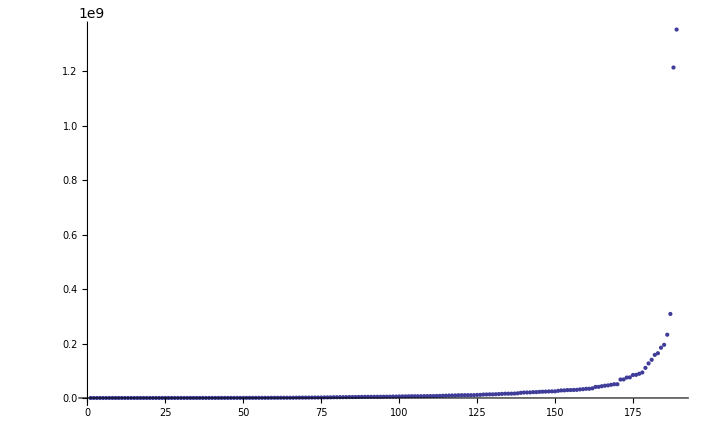

```mathematica
ListPlot[Sort[Table[CountryData[j,"Population"],{j,Flatten[Table[Table[i,{i,CountryData[c]}],{c,Select[CountryData["Continents"],((#≠"Antarctica")&&(#≠"Europe")) &]}]]}]],PlotRange->All]
```

```mathematica
Grid[Reverse[Sort[Table[{CountryData[j,"Population"],j},{j,Flatten[Table[Table[i,{i,CountryData[c]}],{c,Select[CountryData["Continents"],((#≠"Antarctica")) &]}]]}]]],Frame->All]
```

1.35415×10^9 | China
1.21446×10^9 | India
3.08746×10^8 | UnitedStates
2.32517×10^8 | Indonesia
1.95423×10^8 | Brazil
1.84753×10^8 | Pakistan
1.64425×10^8 | Bangladesh
1.58259×10^8 | Nigeria
1.40367×10^8 | Russia
1.26995×10^8 | Japan
1.10645×10^8 | Mexico
9.3617×10^7 | Philippines
8.9029×10^7 | Vietnam
8.4976×10^7 | Ethiopia
8.4474×10^7 | Egypt
8.2057×10^7 | Germany
7.5705×10^7 | Turkey
7.5078×10^7 | Iran
6.8139×10^7 | Thailand
6.7827×10^7 | DemocraticRepublicCongo
6.47684×10^7 | France
6.1899×10^7 | UnitedKingdom
6.0098×10^7 | Italy
5.0496×10^7 | Myanmar
5.0492×10^7 | SouthAfrica
4.8501×10^7 | SouthKorea
4.63×10^7 | Colombia
4.5433×10^7 | Ukraine
4.5317×10^7 | Spain
4.504×10^7 | Tanzania
4.3192×10^7 | Sudan
4.0863×10^7 | Kenya
4.0666×10^7 | Argentina
3.8038×10^7 | Poland
3.5423×10^7 | Algeria
3.389×10^7 | Canada
3.3796×10^7 | Uganda
3.2381×10^7 | Morocco
3.1467×10^7 | Iraq
2.9853×10^7 | Nepal
2.9496×10^7 | Peru
2.9117×10^7 | Afghanistan
2.9044×10^7 | Venezuela
2.7914×10^7 | Malaysia
2.7794×10^7 | Uzbekistan
2.6246×10^7 | SaudiArabia
2.4333×10^7 | Ghana
2.4256×10^7 | Yemen
2.3991×10^7 | NorthKorea
2.3406×10^7 | Mozambique
2.3025×10^7 | Taiwan
2.2505×10^7 | Syria
2.1571×10^7 | IvoryCoast
2.1512×10^7 | Australia
2.119×10^7 | Romania
2.041×10^7 | SriLanka
2.0146×10^7 | Madagascar
1.9958×10^7 | Cameroon
1.8993×10^7 | Angola
1.7135×10^7 | Chile
1.6653×10^7 | Netherlands
1.6287×10^7 | BurkinaFaso
1.5891×10^7 | Niger
1.5753×10^7 | Kazakhstan
1.5692×10^7 | Malawi
1.5053×10^7 | Cambodia
1.4377×10^7 | Guatemala
1.3775×10^7 | Ecuador
1.3323×10^7 | Mali
1.3257×10^7 | Zambia
1.2861×10^7 | Senegal
1.2644×10^7 | Zimbabwe
1.1506×10^7 | Chad
1.1204×10^7 | Cuba
1.1183×10^7 | Greece
1.0732×10^7 | Portugal
1.0698×10^7 | Belgium
1.0411×10^7 | CzechRepublic
1.0374×10^7 | Tunisia
1.0324×10^7 | Guinea
1.0277×10^7 | Rwanda
1.0225×10^7 | DominicanRepublic
1.0188×10^7 | Haiti
1.0031×10^7 | Bolivia
9.973×10^6 | Hungary
9.588×10^6 | Belarus
9.359×10^6 | Somalia
9.293×10^6 | Sweden
9.212×10^6 | Benin
8.934×10^6 | Azerbaijan
8.519×10^6 | Burundi
8.387×10^6 | Austria
8.26049×10^6 | SouthSudan
7.616×10^6 | Honduras
7.595×10^6 | Switzerland
7.497×10^6 | Bulgaria
7.34485×10^6 | Serbia
7.285×10^6 | Israel
7.075×10^6 | Tajikistan
7.069×10^6 | HongKong
6.888×10^6 | PapuaNewGuinea
6.78×10^6 | Togo
6.546×10^6 | Libya
6.472×10^6 | Jordan
6.46×10^6 | Paraguay
6.436×10^6 | Laos
6.194×10^6 | ElSalvador
5.836×10^6 | SierraLeone
5.822×10^6 | Nicaragua
5.55×10^6 | Kyrgyzstan
5.481×10^6 | Denmark
5.412×10^6 | Slovakia
5.346×10^6 | Finland
5.224×10^6 | Eritrea
5.177×10^6 | Turkmenistan
4.855×10^6 | Norway
4.837×10^6 | Singapore
4.707×10^6 | UnitedArabEmirates
4.64×10^6 | CostaRica
4.589×10^6 | Ireland
4.506×10^6 | CentralAfricanRepublic
4.41×10^6 | Croatia
4.409×10^6 | WestBank
4.303×10^6 | NewZealand
4.255×10^6 | Lebanon
4.219×10^6 | Georgia
4.102×10^6 | Liberia
3.998×10^6 | PuertoRico
3.76×10^6 | BosniaHerzegovina
3.759×10^6 | RepublicCongo
3.576×10^6 | Moldova
3.508×10^6 | Panama
3.372×10^6 | Uruguay
3.366×10^6 | Mauritania
3.255×10^6 | Lithuania
3.169×10^6 | Albania
3.09×10^6 | Armenia
3.051×10^6 | Kuwait
2.905×10^6 | Oman
2.73×10^6 | Jamaica
2.701×10^6 | Mongolia
2.42453×10^6 | Kosovo
2.24×10^6 | Latvia
2.212×10^6 | Namibia
2.084×10^6 | Lesotho
2.043×10^6 | Macedonia
2.025×10^6 | Slovenia
1.978×10^6 | Botswana
1.751×10^6 | Gambia
1.647×10^6 | GuineaBissau
1.60424×10^6 | GazaStrip
1.508×10^6 | Qatar
1.501×10^6 | Gabon
1.344×10^6 | TrinidadTobago
1.339×10^6 | Estonia
1.297×10^6 | Mauritius
1.202×10^6 | Swaziland
1.171×10^6 | EastTimor
879000. | Djibouti
854000. | Fiji
807000. | Bahrain
806000. | Reunion
786873. | Cyprus
761000. | Guyana
708000. | Bhutan
693000. | EquatorialGuinea
691000. | Comoros
626000. | Montenegro
548000. | Macau
536000. | SolomonIslands
524000. | Suriname
513000. | CapeVerde
492000. | Luxembourg
467000. | Guadeloupe
416758. | WesternSahara
410000. | Malta
407000. | Brunei
400000. | Martinique
346000. | Bahamas
329000. | Iceland
314000. | Maldives
313000. | Belize
272000. | FrenchPolynesia
257000. | Barbados
254000. | NewCaledonia
246000. | Vanuatu
231139. | Mayotte
231000. | FrenchGuiana
180000. | Guam
179000. | Samoa
174000. | SaintLucia
165000. | SaoTomePrincipe
140794. | Curacao
111000. | Micronesia
109000. | UnitedStatesVirginIslands
109000. | SaintVincentGrenadines
107000. | Aruba
104000. | Tonga
104000. | Grenada
100000. | Kiribati
91812. | Jersey
89000. | AntiguaBarbuda
88000. | NorthernMarianaIslands
87000. | Andorra
85000. | Seychelles
76913. | IsleOfMan
67000. | Dominica
66432. | AmericanSamoa
65632. | Guernsey
65000. | Bermuda
63000. | MarshallIslands
57000. | Greenland
57000. | CaymanIslands
52000. | SaintKittsNevis
50000. | FaroeIslands
37429. | SintMaarten
36000. | Liechtenstein
33000. | TurksCaicosIslands
33000. | Monaco
32000. | SanMarino
28877. | Gibraltar
23000. | BritishVirginIslands
21000. | Palau
20000. | CookIslands
15343. | WallisFutuna
15000. | Anguilla
10000. | Tuvalu
10000. | Nauru
7670. | SaintHelena
7070. | SaintPierreMiquelon
6000. | Montserrat
3140. | FalklandIslands
2495. | Svalbard
2141. | NorfolkIsland
1462. | ChristmasIsland
1416. | Tokelau
1000. | Niue
826. | VaticanCity
605. | CocosKeelingIslands
48. | PitcairnIslands